```mathematica
(*Set your directory to where the mathematica notebook is saved*)
SetDirectory[NotebookDirectory[]];
```

## Useful functions for extracting data

```mathematica
ColPos[table_,heading_]:=Position[table[[1]],heading][[1,1]];(*given a table, and a heading name, this gives the column it refers to*)
```

```mathematica
ColDat[table_,heading_]:=table[[;;,ColPos[table,heading]]];(*given a table and heading name, this returns the whole column*)
```

```mathematica
RowPos[table_,columnName_,entry_]:=Position[table[[;;,ColPos[table,columnName]]],entry];(*for a given table and heading name, this gives the row numbers in which entry is found*)
```

```mathematica
RowDat[table_,columnNameIn_,entry_]:=Extract[table,Join[{{1}},RowPos[table,columnNameIn,entry]]];(*for rows matching entry in columnNameIn in table, output the corresponding rows of table. Keeps the header row*)
```

```mathematica
RowDat[table_,columnNameOut_,columnNameIn_,entry_]:=Extract[table[[;;,ColPos[table,columnNameOut]]],RowPos[table,columnNameIn,entry]];(*for rows matching entry in columnNameIn in table, output the entries in columbNameOut*)
```

## Number of fully vaccinated individuals per country

```mathematica
(*import vaccination data from Our World in Data*)
```

```mathematica
vaccination=Import["OWD_data.xlsx"][[1]];
```

```mathematica
(*extract the data for a given country
(*Argentina*)
(*Bahrain*)
(*Bangladesh*)
(*Bolivia*)
(*Iran*)
(*Montenegro*)
(*Nepal*)
(*Sri Lanka*)
(*Turkey*)
*)
```

```mathematica
(*Here, we select Turkey as an example*)
```

```mathematica
data=RowDat[vaccination,"location",n_/;MemberQ[{"","Turkey"},n]];
```

```mathematica
data[[1;;10]]//MatrixForm
```

(iso_code | continent | location | date | total_cases | new_cases | new_cases_smoothed | total_deaths | new_deaths | new_deaths_smoothed | total_cases_per_million | new_cases_per_million | new_cases_smoothed_per_million | total_deaths_per_million | new_deaths_per_million | new_deaths_smoothed_per_million | reproduction_rate | icu_patients | icu_patients_per_million | hosp_patients | hosp_patients_per_million | weekly_icu_admissions | weekly_icu_admissions_per_million | weekly_hosp_admissions | weekly_hosp_admissions_per_million | total_tests | new_tests | total_tests_per_thousand | new_tests_per_thousand | new_tests_smoothed | new_tests_smoothed_per_thousand | positive_rate | tests_per_case | tests_units | total_vaccinations | people_vaccinated | people_fully_vaccinated | total_boosters | new_vaccinations | new_vaccinations_smoothed | total_vaccinations_per_hundred | people_vaccinated_per_hundred | people_fully_vaccinated_per_hundred | total_boosters_per_hundred | new_vaccinations_smoothed_per_million | new_people_vaccinated_smoothed | new_people_vaccinated_smoothed_per_hundred | stringency_index | population_density | median_age | aged_65_older | aged_70_older | gdp_per_capita | extreme_poverty | cardiovasc_death_rate | diabetes_prevalence | female_smokers | male_smokers | handwashing_facilities | hospital_beds_per_thousand | life_expectancy | human_development_index | population | excess_mortality_cumulative_absolute | excess_mortality_cumulative | excess_mortality | excess_mortality_cumulative_per_million
TUR | Asia | Turkey | 2020-03-11 | 1. | 1. |  |  |  |  | 0.012 | 0.012 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 23.15 | 104.914 | 31.6 | 8.153 | 5.061 | 25129.3 | 0.2 | 171.285 | 12.13 | 14.1 | 41.1 |  | 2.81 | 77.69 | 0.82 | 8.53412×10^7 |  |  |  | 
TUR | Asia | Turkey | 2020-03-12 | 1. | 0. |  |  |  |  | 0.012 | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 23.15 | 104.914 | 31.6 | 8.153 | 5.061 | 25129.3 | 0.2 | 171.285 | 12.13 | 14.1 | 41.1 |  | 2.81 | 77.69 | 0.82 | 8.53412×10^7 |  |  |  | 
TUR | Asia | Turkey | 2020-03-13 | 5. | 4. |  |  |  |  | 0.059 | 0.047 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 23.15 | 104.914 | 31.6 | 8.153 | 5.061 | 25129.3 | 0.2 | 171.285 | 12.13 | 14.1 | 41.1 |  | 2.81 | 77.69 | 0.82 | 8.53412×10^7 |  |  |  | 
TUR | Asia | Turkey | 2020-03-14 | 5. | 0. |  |  |  |  | 0.059 | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 23.15 | 104.914 | 31.6 | 8.153 | 5.061 | 25129.3 | 0.2 | 171.285 | 12.13 | 14.1 | 41.1 |  | 2.81 | 77.69 | 0.82 | 8.53412×10^7 |  |  |  | 
TUR | Asia | Turkey | 2020-03-15 | 6. | 1. |  |  |  |  | 0.07 | 0.012 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 23.15 | 104.914 | 31.6 | 8.153 | 5.061 | 25129.3 | 0.2 | 171.285 | 12.13 | 14.1 | 41.1 |  | 2.81 | 77.69 | 0.82 | 8.53412×10^7 |  |  |  | 
TUR | Asia | Turkey | 2020-03-16 | 18. | 12. | 2.571 |  |  |  | 0.211 | 0.141 | 0.03 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 52.78 | 104.914 | 31.6 | 8.153 | 5.061 | 25129.3 | 0.2 | 171.285 | 12.13 | 14.1 | 41.1 |  | 2.81 | 77.69 | 0.82 | 8.53412×10^7 |  |  |  | 
TUR | Asia | Turkey | 2020-03-17 | 47. | 29. | 6.714 | 1. | 1. |  | 0.551 | 0.34 | 0.079 | 0.012 | 0.012 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 52.78 | 104.914 | 31.6 | 8.153 | 5.061 | 25129.3 | 0.2 | 171.285 | 12.13 | 14.1 | 41.1 |  | 2.81 | 77.69 | 0.82 | 8.53412×10^7 |  |  |  | 
TUR | Asia | Turkey | 2020-03-18 | 98. | 51. | 13.857 | 1. | 0. |  | 1.148 | 0.598 | 0.162 | 0.012 | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 58.33 | 104.914 | 31.6 | 8.153 | 5.061 | 25129.3 | 0.2 | 171.285 | 12.13 | 14.1 | 41.1 |  | 2.81 | 77.69 | 0.82 | 8.53412×10^7 |  |  |  | 
TUR | Asia | Turkey | 2020-03-19 | 192. | 94. | 27.286 | 3. | 2. |  | 2.25 | 1.101 | 0.32 | 0.035 | 0.023 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 58.33 | 104.914 | 31.6 | 8.153 | 5.061 | 25129.3 | 0.2 | 171.285 | 12.13 | 14.1 | 41.1 |  | 2.81 | 77.69 | 0.82 | 8.53412×10^7 |  |  |  | )

```mathematica
(*extract the reported number of fully vaccinated individuals for a given country*)
```

```mathematica
fullVaccinatedRaw=MapThread[List,{FromDateString[ColDat[data,"date"][[2;;]]],ColDat[data,"people_fully_vaccinated"][[2;;]]}];
fullVaccinated={};
For[i=1,i<=Length[fullVaccinatedRaw],i++,If[fullVaccinatedRaw[[i,2]]!="",AppendTo[fullVaccinated,fullVaccinatedRaw[[i]]]]];
```

```mathematica
(*find the start and end dates of the vaccination data*)
```

```mathematica
For[i=1,i<=Length[fullVaccinated],i++,If[fullVaccinated[[i,2]]!=0&&fullVaccinated[[i,2]]!="",start=QuantityMagnitude[DateDifference[FromDateString["2020-01-01"],fullVaccinated[[i,1]]]];Break[]]];
end=QuantityMagnitude[DateDifference[FromDateString["2020-01-01"],fullVaccinated[[-1,1]]]];
```

```mathematica
(*fill in any timepoints with missing data using a first degree polynomial approximation*)
```

```mathematica
fullVaccinatedc=Evaluate@Interpolation[Table[{QuantityMagnitude[DateDifference[FromDateString["2020-01-01"],fullVaccinated[[i,1]]]],fullVaccinated[[i,2]]},{i,1,Length[fullVaccinated]}],InterpolationOrder->1][x];
fullVaccinated=Table[{Quantity[i,"Days"],fullVaccinatedc/.x->i},{i,start,end}];
fullVaccinated=Join[Table[{Quantity[i,"Days"],0},{i,1,start-1}],fullVaccinated];
```

```mathematica
(*make a list of daily number of fully vaccinated individuals*)
```

```mathematica
fullVaccinated=Table[{fullVaccinated[[i,1]],fullVaccinated[[i,2]]-fullVaccinated[[i-1,2]]},{i,2,Length[fullVaccinated]}];
```

```mathematica
(*rescale the daily number of fully vaccinated individuals in a model country to Iran's population*)
```

```mathematica
fullVaccinated=Table[{fullVaccinated[[i,1]],fullVaccinated[[i,2]]/(ColDat[data,"population"][[2]])*8.8550568*^7},{i,1,Length[fullVaccinated]}];
```

```mathematica
(*export the modified trajectory of fully vaccinated individuals for a given country (here for turkey)*)
```

```mathematica
Export["turkey_fullyvaxed.txt",fullVaccinated];
```

```mathematica
(*cut the data to only include dates from 19 jul 2020 to 20 apr 2022*)
count1=0;
count2=0;
For[i=1,i<=Length[fullVaccinated],i++,
If[QuantityMagnitude[fullVaccinated[[i,1]]]==200,count1=i];
If[QuantityMagnitude[fullVaccinated[[i,1]]]==840,count2=i]];
fullVaccinated=fullVaccinated[[count1;;count2]];
```

## Distribution of fully vaccinated individuals per age group

```mathematica
(*import the age distribution of the iranian population*)
ageDistribution=Import["iran's demography from 1398 to 1400 solar hijri.xlsx"];
ageDistribution=ageDistribution[[1]][[2;;]];
ageDistributionprovince1=Table[Transpose[ageDistribution][[2]][[1+(i-1)*21;;i*21]][[4;;-1]],{i,1,32}];
ageDistributionprovince=Table[Transpose[ageDistribution][[2]][[1+(i-1)*21;;i*21]][[4;;-1]],{i,2,32}];
AppendTo[ageDistributionprovince,ageDistributionprovince1[[1]]];
```

```mathematica
count=0;
vaxgroups={};(*stores the number of fully vaccinated individuals per age group {+80,+75,+70,+65,+69,+55,+50, 5<=x<50}*)

For[i=1,i<=Length[fullVaccinated],i++,

If[fullVaccinated[[i,2]]>0,count++];

(*allocate number of fully vaccinated individuals based on a descending age group order*)
If[count<QuantityMagnitude[DateDifference[FromDateString["2021-05-08"],FromDateString["2021-05-18"]]],
AppendTo[vaxgroups,Round[MapThread[Times,{{1,0,0,0,0,0,0,0},Reverse[ageDistributionprovince[[32,-9;;-2]]]/Total[ageDistributionprovince[[32,-2]]]}]*fullVaccinated[[i,2]]]]
];

If[QuantityMagnitude[DateDifference[FromDateString["2021-05-08"],FromDateString["2021-05-18"]]]<=count<QuantityMagnitude[DateDifference[FromDateString["2021-05-08"],FromDateString["2021-05-22"]]],
AppendTo[vaxgroups,Round[MapThread[Times,{{1,1,0,0,0,0,0,0},Reverse[ageDistributionprovince[[32,-9;;-2]]]/Total[ageDistributionprovince[[32,-3;;-2]]]}]*fullVaccinated[[i,2]]]];
];

If[QuantityMagnitude[DateDifference[FromDateString["2021-05-08"],FromDateString["2021-05-22"]]]<=count<QuantityMagnitude[DateDifference[FromDateString["2021-05-08"],FromDateString["2021-07-11"]]],
AppendTo[vaxgroups,Round[MapThread[Times,{{1,1,1,0,0,0,0,0},Reverse[ageDistributionprovince[[32,-9;;-2]]]/Total[ageDistributionprovince[[32,-4;;-2]]]}]*fullVaccinated[[i,2]]]];
];

If[QuantityMagnitude[DateDifference[FromDateString["2021-05-08"],FromDateString["2021-07-11"]]]<=count<QuantityMagnitude[DateDifference[FromDateString["2021-05-08"],FromDateString["2021-07-14"]]],
AppendTo[vaxgroups,Round[MapThread[Times,{{1,1,1,1,0,0,0,0},Reverse[ageDistributionprovince[[32,-9;;-2]]]/Total[ageDistributionprovince[[32,-5;;-2]]]}]*fullVaccinated[[i,2]]]];
];

If[QuantityMagnitude[DateDifference[FromDateString["2021-05-08"],FromDateString["2021-07-14"]]]<=count<QuantityMagnitude[DateDifference[FromDateString["2021-05-08"],FromDateString["2021-07-24"]]],
AppendTo[vaxgroups,Round[MapThread[Times,{{1,1,1,1,1,0,0,0},Reverse[ageDistributionprovince[[32,-9;;-2]]]/Total[ageDistributionprovince[[32,-6;;-2]]]}]*fullVaccinated[[i,2]]]];
];

If[QuantityMagnitude[DateDifference[FromDateString["2021-05-08"],FromDateString["2021-07-24"]]]<=count<QuantityMagnitude[DateDifference[FromDateString["2021-05-08"],FromDateString["2021-07-30"]]],
AppendTo[vaxgroups,Round[MapThread[Times,{{1,1,1,1,1,1,0,0},Reverse[ageDistributionprovince[[32,-9;;-2]]]/Total[ageDistributionprovince[[32,-7;;-2]]]}]*fullVaccinated[[i,2]]]];
];

If[QuantityMagnitude[DateDifference[FromDateString["2021-05-08"],FromDateString["2021-07-30"]]]<=count<QuantityMagnitude[DateDifference[FromDateString["2021-05-08"],FromDateString["2021-08-03"]]],
AppendTo[vaxgroups,Round[MapThread[Times,{{1,1,1,1,1,1,1,0},Reverse[ageDistributionprovince[[32,-9;;-2]]]/Total[ageDistributionprovince[[32,-8;;-2]]]}]*fullVaccinated[[i,2]]]];
];

If[count>=QuantityMagnitude[DateDifference[FromDateString["2021-05-08"],FromDateString["2021-08-03"]]],
AppendTo[vaxgroups,Round[MapThread[Times,{{1,1,1,1,1,1,1,1},Reverse[Join[{Total[ageDistributionprovince[[32,2;;-9]]]},ageDistributionprovince[[32,-8;;-2]]]]/Total[ageDistributionprovince[[32,2;;-2]]]}]*fullVaccinated[[i,2]]]];
];

(*if the number of fully vaccinated individuals gets larger than the total population size of a certain age group, re-distribute the remainder to the other age-groups*);
If[Count[Table[Total[vaxgroups[[;;,j]]]>1000*ageDistributionprovince[[32,-j-1]],{j,1,7}],True]>0,
pos=Flatten[Position[Table[Total[vaxgroups[[;;,j]]]>1000*ageDistributionprovince[[32,-j-1]],{j,1,7}],True]];
diff=0;
For[k=1,k<=Length[pos],k++,
diff=diff+Total[vaxgroups[[;;,pos[[k]]]]]-1000*ageDistributionprovince[[32,-pos[[k]]-1]];
vaxgroups[[-1,pos[[k]]]]=1000*ageDistributionprovince[[32,-pos[[k]]-1]]-(Total[vaxgroups[[;;-2,pos[[k]]]]]);
];
For[l=1,l<=Length[Complement[Table[o,{o,1,8}],pos]],l++,
vaxgroups[[-1,Complement[Table[o,{o,1,8}],pos][[l]]]]=vaxgroups[[-1,Complement[Table[o,{o,1,8}],pos][[l]]]]+diff*Reverse[Join[{Total[ageDistributionprovince[[32,2;;-9]]]},ageDistributionprovince[[32,-8;;-2]]]][[Complement[Table[o,{o,1,8}],pos][[l]]]]/Total[Reverse[Join[{Total[ageDistributionprovince[[32,2;;-9]]]},ageDistributionprovince[[32,-8;;-2]]]][[Complement[Table[o,{o,1,8}],pos]]]];
];
];

For[p=1,p<=Length[vaxgroups[[1]]],p++,
If[vaxgroups[[-1,p]]<0,vaxgroups[[-1,p]]=0]
]

]
```

```mathematica
(*export factual/counterfactual vaccine roll-out per age group (here for turkey)*)
```

```mathematica
Export["turkey_vax_pergroup2.txt",vaxgroups];
```

## Calculate excess vaccination per age group

```mathematica
(*import list of fully vaccinated individuals for Iran and a model country (here for turkey) for all age groups*)
```

```mathematica
vaxgroupsIran=ReadList["iran_vax_pergroup2.txt"];
vaxgroupsModelCountry=ReadList["turkey_vax_pergroup2.txt"];
```

```mathematica
(*calculate net difference in vaccination per age group between the model country and Iran*)
```

```mathematica
excessVaccines={Table[Sum[vaxgroupsModelCountry[[;;,1]][[j]]-vaxgroupsIran[[;;,1]][[j]],{j,1,i}],{i,1,Length[vaxgroupsModelCountry[[;;,1]]]}],Table[Sum[vaxgroupsModelCountry[[;;,2]][[j]]-vaxgroupsIran[[;;,2]][[j]],{j,1,i}],{i,1,Length[vaxgroupsModelCountry[[;;,2]]]}],Table[Sum[vaxgroupsModelCountry[[;;,3]][[j]]-vaxgroupsIran[[;;,3]][[j]],{j,1,i}],{i,1,Length[vaxgroupsModelCountry[[;;,3]]]}],Table[Sum[vaxgroupsModelCountry[[;;,4]][[j]]-vaxgroupsIran[[;;,4]][[j]],{j,1,i}],{i,1,Length[vaxgroupsModelCountry[[;;,4]]]}],Table[Sum[vaxgroupsModelCountry[[;;,5]][[j]]-vaxgroupsIran[[;;,5]][[j]],{j,1,i}],{i,1,Length[vaxgroupsModelCountry[[;;,5]]]}],Table[Sum[vaxgroupsModelCountry[[;;,6]][[j]]-vaxgroupsIran[[;;,6]][[j]],{j,1,i}],{i,1,Length[vaxgroupsModelCountry[[;;,6]]]}],Table[Sum[vaxgroupsModelCountry[[;;,7]][[j]]-vaxgroupsIran[[;;,7]][[j]],{j,1,i}],{i,1,Length[vaxgroupsModelCountry[[;;,7]]]}],Table[Sum[vaxgroupsModelCountry[[;;,8]][[j]]-vaxgroupsIran[[;;,8]][[j]],{j,1,i}],{i,1,Length[vaxgroupsModelCountry[[;;,8]]]}]};
```

```mathematica
(*proportion of excess vaccination per age group*)
```

```mathematica
proportionofexcessVax=Table[excessVaccines[[i]]/(Reverse[Join[{Total[ageDistributionprovince[[32,2;;-9]]]},ageDistributionprovince[[32,-8;;-2]]]][[i]]*1000),{i,1,8}];
```

```mathematica
(*prepend 0 excess vaccination for days before the start of vaccination in the the country with the earlier roll-out date*)
```

```mathematica
For[i=200,i>=1,i--,PrependTo[proportionofexcessVax[[1]],0];PrependTo[proportionofexcessVax[[2]],0];PrependTo[proportionofexcessVax[[3]],0];PrependTo[proportionofexcessVax[[4]],0];PrependTo[proportionofexcessVax[[5]],0];PrependTo[proportionofexcessVax[[6]],0];PrependTo[proportionofexcessVax[[7]],0];PrependTo[proportionofexcessVax[[8]],0]];
```

```mathematica
(*convert daily proportions to weekly proportions*)
```

```mathematica
adjustpropVax=Table[proportionofexcessVax[[i]][[j]],{i,1,8},{j,1,840,7}];
```

## Calculate the number of avertable deaths per age group

```mathematica
(*import excess mortality data*)
```

```mathematica
mortality=Import["age_province_excess_deaths_20221016.csv"];
```

```mathematica
provinceExcessDeathsMean=Table[Transpose[mortality]⟦-3⟧⟦2+i*2482;;2+(i+1)*2482-1⟧,{i,0,31}];
```

```mathematica
(*calculate the one-month average of weekly excess mortality*)
```

```mathematica
window=4;
ageStratifiedMortality={};
For[i=1,i≤32,i++,
provinceNumber=i;
mortalityAge=
Table[Flatten[Partition[Partition[provinceExcessDeathsMean⟦provinceNumber⟧⟦1;;17*146⟧,window,1,1,{},Mean[{##}]&],146][[i]],1][[1;;]],{i,1,17}];
AppendTo[ageStratifiedMortality,{mortalityAge⟦1⟧,mortalityAge⟦10⟧,mortalityAge⟦2⟧,mortalityAge⟦3⟧,mortalityAge⟦4⟧,mortalityAge⟦5⟧,mortalityAge⟦6⟧,mortalityAge⟦7⟧,mortalityAge⟦8⟧,mortalityAge⟦9⟧,mortalityAge⟦11⟧,mortalityAge⟦12⟧,mortalityAge⟦13⟧,mortalityAge⟦14⟧,mortalityAge⟦15⟧,mortalityAge⟦16⟧,mortalityAge⟦17⟧,Plus@@(mortalityAge⟦All⟧)}]];
```

```mathematica
(*calculate the excess mortality per age group for the designated age groups {+80,+75,+70,+65,+69,+55,+50, 5<=x<50}*)
```

```mathematica
excessDeathspergroup={(ageStratifiedMortality[[provinceNumber]]/._?Negative->0)[[-2]],(ageStratifiedMortality[[provinceNumber]]/._?Negative->0)[[-3]],(ageStratifiedMortality[[provinceNumber]]/._?Negative->0)[[-4]],(ageStratifiedMortality[[provinceNumber]]/._?Negative->0)[[-5]],(ageStratifiedMortality[[provinceNumber]]/._?Negative->0)[[-6]],(ageStratifiedMortality[[provinceNumber]]/._?Negative->0)[[-7]],(ageStratifiedMortality[[provinceNumber]]/._?Negative->0)[[-8]],Map[Total,Transpose[(ageStratifiedMortality[[provinceNumber]]/._?Negative->0)[[3;;10]]]]};
```

```mathematica
(*cacluate an expected, upper, and lower bound for the excess mortality under counterfactual roll-out based on model country*)
adjustedexcessDeathspergroup=excessDeathspergroup;
adjustedexcessDeathspergrouplow=excessDeathspergroup;
adjustedexcessDeathspergrouphigh=excessDeathspergroup;
For[i=1,i<=8,i++,
For[j=3,j<=120,j++,
If[adjustpropVax[[i,j-2]]>0&&i<=5,adjustedexcessDeathspergroup[[i,j]]=(1-adjustpropVax[[i,j-2]])excessDeathspergroup[[i,j]]+adjustpropVax[[i,j-2]]*excessDeathspergroup[[i,j]]*(1-0.801);
adjustedexcessDeathspergrouplow[[i,j]]=(1-adjustpropVax[[i,j-2]])excessDeathspergroup[[i,j]]+adjustpropVax[[i,j-2]]*excessDeathspergroup[[i,j]]*(1-0.611);
adjustedexcessDeathspergrouphigh[[i,j]]=(1-adjustpropVax[[i,j-2]])excessDeathspergroup[[i,j]]+adjustpropVax[[i,j-2]]*excessDeathspergroup[[i,j]]*(1-0.898);];

If[adjustpropVax[[i,j-2]]>0&&i>5,adjustedexcessDeathspergroup[[i,j]]=(1-adjustpropVax[[i,j-2]])excessDeathspergroup[[i,j]]+adjustpropVax[[i,j-2]]*excessDeathspergroup[[i,j]]*(1-0.923);
adjustedexcessDeathspergrouplow[[i,j]]=(1-adjustpropVax[[i,j-2]])excessDeathspergroup[[i,j]]+adjustpropVax[[i,j-2]]*excessDeathspergroup[[i,j]]*(1-0.672);
adjustedexcessDeathspergrouphigh[[i,j]]=(1-adjustpropVax[[i,j-2]])excessDeathspergroup[[i,j]]+adjustpropVax[[i,j-2]]*excessDeathspergroup[[i,j]]*(1-0.982);];

If[adjustpropVax[[i,j-2]]<0&&i<=5,adjustedexcessDeathspergroup[[i,j]]=(1-adjustpropVax[[i,j-2]])excessDeathspergroup[[i,j]]-adjustpropVax[[i,j-2]]*excessDeathspergroup[[i,j]]/(1-0.801);
adjustedexcessDeathspergrouplow[[i,j]]=(1-adjustpropVax[[i,j-2]])excessDeathspergroup[[i,j]]-adjustpropVax[[i,j-2]]*excessDeathspergroup[[i,j]]/(1-0.611);
adjustedexcessDeathspergrouphigh[[i,j]]=(1-adjustpropVax[[i,j-2]])excessDeathspergroup[[i,j]]-adjustpropVax[[i,j-2]]*excessDeathspergroup[[i,j]]/(1-0.898)];

If[adjustpropVax[[i,j-2]]<0&&i>5,adjustedexcessDeathspergroup[[i,j]]=(1-adjustpropVax[[i,j-2]])excessDeathspergroup[[i,j]]-adjustpropVax[[i,j-2]]*excessDeathspergroup[[i,j]]/(1-0.923);
adjustedexcessDeathspergrouplow[[i,j]]=(1-adjustpropVax[[i,j-2]])excessDeathspergroup[[i,j]]-adjustpropVax[[i,j-2]]*excessDeathspergroup[[i,j]]/(1-0.672);
adjustedexcessDeathspergrouphigh[[i,j]]=(1-adjustpropVax[[i,j-2]])excessDeathspergroup[[i,j]]-adjustpropVax[[i,j-2]]*excessDeathspergroup[[i,j]]/(1-0.982)];
]
]
```

```mathematica
Print["Overall"]
avertableDeaths=Table[Total[excessDeathspergroup[[i]][[;;120]]-adjustedexcessDeathspergroup[[i]][[;;120]]],{i,1,8}];
avertableDeathslow=Table[Total[excessDeathspergroup[[i]][[;;120]]-adjustedexcessDeathspergrouplow[[i]][[;;120]]],{i,1,8}];
avertableDeathshigh=Table[Total[excessDeathspergroup[[i]][[;;120]]-adjustedexcessDeathspergrouphigh[[i]][[;;120]]],{i,1,8}];

Print["Cumulative"]
Round[Total[avertableDeaths],100]
Round[Total[avertableDeathslow],100]
Round[Total[avertableDeathshigh],100]
Print["Above 50"]
Round[Total[avertableDeaths[[;;7]]],100]
Round[Total[avertableDeathslow[[;;7]]],100]
Round[Total[avertableDeathshigh[[;;7]]],100]
Print["Below 50"]
Round[Total[avertableDeaths[[-1]]],100]
Round[Total[avertableDeathslow[[-1]]],100]
Round[Total[avertableDeathshigh[[-1]]],100]
```

Overall

Cumulative

50000

38100

53500

Above 50

46200

35100

51500

Below 50

3800

3100

2100

```mathematica
Print["Up to the end of Delta"]
avertableDeaths=Table[Total[excessDeathspergroup[[i]][[;;103]]-adjustedexcessDeathspergroup[[i]][[;;103]]],{i,1,8}];
avertableDeathslow=Table[Total[excessDeathspergroup[[i]][[;;103]]-adjustedexcessDeathspergrouplow[[i]][[;;103]]],{i,1,8}];
avertableDeathshigh=Table[Total[excessDeathspergroup[[i]][[;;103]]-adjustedexcessDeathspergrouphigh[[i]][[;;103]]],{i,1,8}];

Print["Cumulative"]
Round[Total[avertableDeaths],100]
Round[Total[avertableDeathslow],100]
Round[Total[avertableDeathshigh],100]
Print["Above 50"]
Round[Total[avertableDeaths[[;;7]]],100]
Round[Total[avertableDeathslow[[;;7]]],100]
Round[Total[avertableDeathshigh[[;;7]]],100]
Print["Below 50"]
Round[Total[avertableDeaths[[-1]]],100]
Round[Total[avertableDeathslow[[-1]]],100]
Round[Total[avertableDeathshigh[[-1]]],100]
```

Up to the end of Delta

Cumulative

50400

38100

55900

Above 50

45900

34800

51200

Below 50

4500

3300

4800

```mathematica
Print["During Omicron"]
avertableDeaths=Table[Total[excessDeathspergroup[[i]][[105;;120]]-adjustedexcessDeathspergroup[[i]][[105;;120]]],{i,1,8}];
avertableDeathslow=Table[Total[excessDeathspergroup[[i]][[105;;120]]-adjustedexcessDeathspergrouplow[[i]][[105;;120]]],{i,1,8}];
avertableDeathshigh=Table[Total[excessDeathspergroup[[i]][[105;;120]]-adjustedexcessDeathspergrouphigh[[i]][[105;;120]]],{i,1,8}];

Print["Cumulative"]
Round[Total[avertableDeaths],100]
Round[Total[avertableDeathslow],100]
Round[Total[avertableDeathshigh],100]
Print["Above 50"]
Round[Total[avertableDeaths[[;;7]]],100]
Round[Total[avertableDeathslow[[;;7]]],100]
Round[Total[avertableDeathshigh[[;;7]]],100]
Print["Below 50"]
Round[Total[avertableDeaths[[-1]]],100]
Round[Total[avertableDeathslow[[-1]]],100]
Round[Total[avertableDeathshigh[[-1]]],100]
```

During Omicron

Cumulative

-400

0

-2400

Above 50

300

200

300

Below 50

-700

-200

-2700

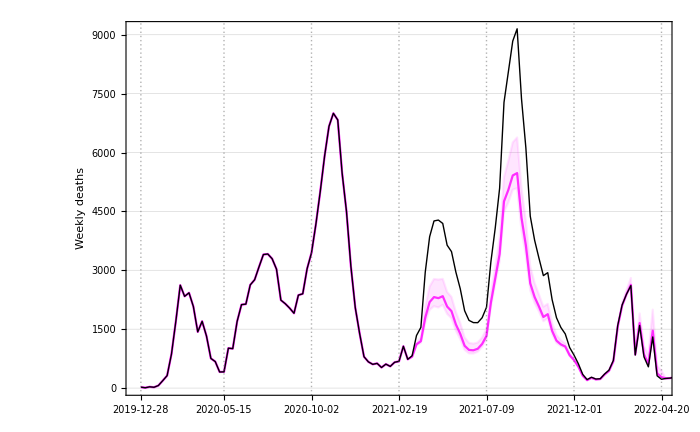

```mathematica
p1=ListPlot[{Map[Total,Transpose[adjustedexcessDeathspergrouphigh]],Map[Total,Transpose[adjustedexcessDeathspergroup]],Map[Total,Transpose[adjustedexcessDeathspergrouplow]],Map[Total,Transpose[excessDeathspergroup]]},Joined->True,PlotRange->{{0,120},All},PlotStyle->{{Magenta,Opacity[0.1]},{Magenta,Opacity[0.8]},{Magenta,Opacity[0.1]},{Black,Thick}},Filling->{1->{3}},FillingStyle->{Magenta,Opacity[0.1]},FrameLabel->{"","Weekly deaths"},LabelStyle->Directive[Black,15],PlotTheme->"Detailed",FrameTicks->{Automatic,{{{1,"2019-12-28"},{20,"2020-05-15"},{40,"2020-10-02"},{60,"2021-02-19"},{80,"2021-07-09"},{100,"2021-12-01"},{120,"2022-04-20"}},Automatic}},ImageSize->700]
```

```mathematica
cumulatives={Table[Sum[Map[Total,Transpose[excessDeathspergroup]][[j]]-Map[Total,Transpose[adjustedexcessDeathspergrouphigh]][[j]],{j,1,i}],{i,1,Length[adjustedexcessDeathspergrouphigh[[1]]]}],Table[Sum[Map[Total,Transpose[excessDeathspergroup]][[j]]-Map[Total,Transpose[adjustedexcessDeathspergroup]][[j]],{j,1,i}],{i,1,Length[adjustedexcessDeathspergrouphigh[[1]]]}],Table[Sum[Map[Total,Transpose[excessDeathspergroup]][[j]]-Map[Total,Transpose[adjustedexcessDeathspergrouplow]][[j]],{j,1,i}],{i,1,Length[adjustedexcessDeathspergrouphigh[[1]]]}]};
```

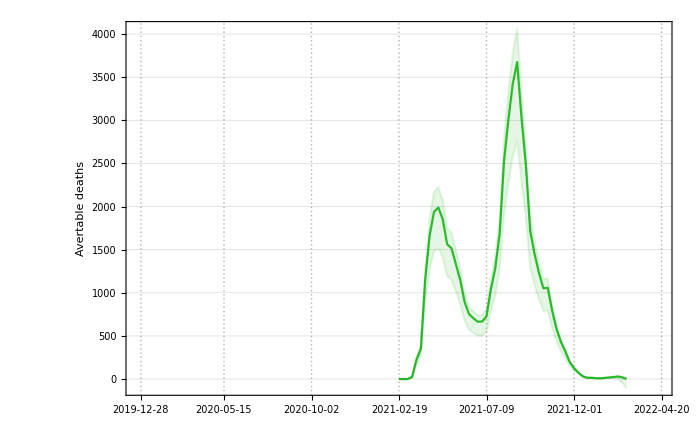

```mathematica
plt1=ListPlot[Table[Table[{j,cumulatives[[i,j]]-cumulatives[[i,j-1]]},{j,60,112}],{i,1,Length[cumulatives]}],Joined->True,PlotRange->{{0,120},All},PlotStyle->{{Darker[Green],Opacity[0.1]},{Darker[Green],Opacity[0.8]},{Darker[Green],Opacity[0.1]}},FillingStyle->Directive[Opacity[0.1],Darker[Green]],Filling->{1->{3}},FrameLabel->{"","Avertable deaths"},LabelStyle->Directive[Black,15],PlotTheme->"Detailed",FrameTicks->{Automatic,{{{1,"2019-12-28"},{20,"2020-05-15"},{40,"2020-10-02"},{60,"2021-02-19"},{80,"2021-07-09"},{100,"2021-12-01"},{120,"2022-04-20"}},Automatic}},ImageSize->700]
```

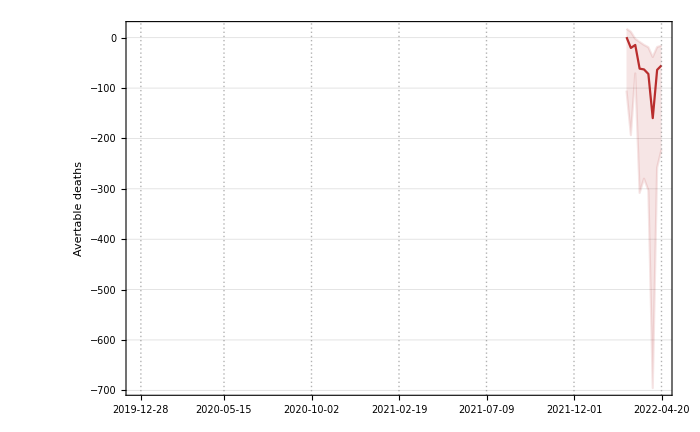

```mathematica
plt2=ListPlot[Table[Table[{j,cumulatives[[i,j]]-cumulatives[[i,j-1]]},{j,112,120}],{i,1,Length[cumulatives]}],Joined->True,PlotRange->{{0,120},All},PlotStyle->{{Darker[Red],Opacity[0.1]},{Darker[Red],Opacity[0.8]},{Darker[Red],Opacity[0.1]}},FillingStyle->Directive[Opacity[0.1],Darker[Red]],Filling->{3->{1}},FrameLabel->{"","Avertable deaths"},LabelStyle->Directive[Black,15],PlotTheme->"Detailed",FrameTicks->{Automatic,{{{1,"2019-12-28"},{20,"2020-05-15"},{40,"2020-10-02"},{60,"2021-02-19"},{80,"2021-07-09"},{100,"2021-12-01"},{120,"2022-04-20"}},Automatic}},ImageSize->700]
```

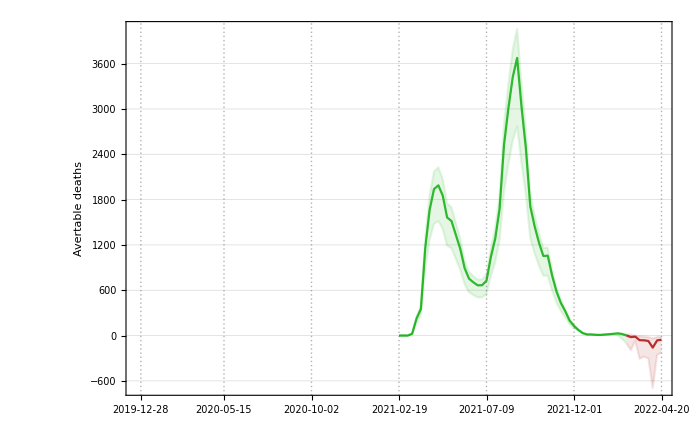

```mathematica
p2=Show[plt1,plt2,PlotRange->{{0,120},All}]
```

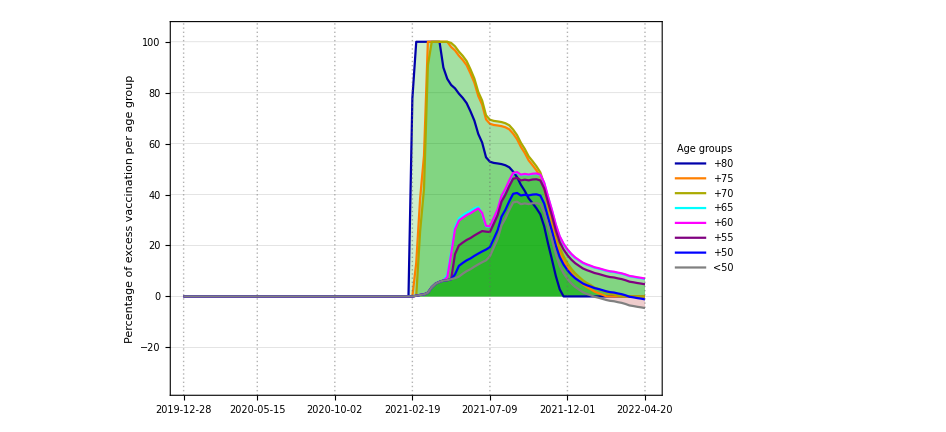

```mathematica
ListPlot[100adjustpropVax,Joined->True,PlotRange->{{0,122},{-36,105.1}},Filling->{1->Axis,2->Axis,3->Axis,4->Axis,5->Axis,6->Axis,7->Axis,8->Axis},FillingStyle->{Directive[Opacity[0.2],Darker[Red]],Directive[Opacity[0.2],Darker[Green]]},PlotStyle->{Darker[Blue],Orange,Darker[Yellow],Cyan,Magenta,Purple,Blue,Gray},PlotTheme->"Detailed",LabelStyle->Directive[Black,15],FrameLabel->{"","Percentage of excess vaccination per age group"},FrameTicks->{Automatic,{{{1,"2019-12-28"},{20,"2020-05-15"},{40,"2020-10-02"},{60,"2021-02-19"},{80,"2021-07-09"},{100,"2021-12-01"},{120,"2022-04-20"}},Automatic}},ImageSize->700,PlotLegends->LineLegend[{"+80","+75","+70","+65","+60","+55","+50","<50"},LegendLabel->"Age groups",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5]]
```

```mathematica
p3=-Graphics-;
```

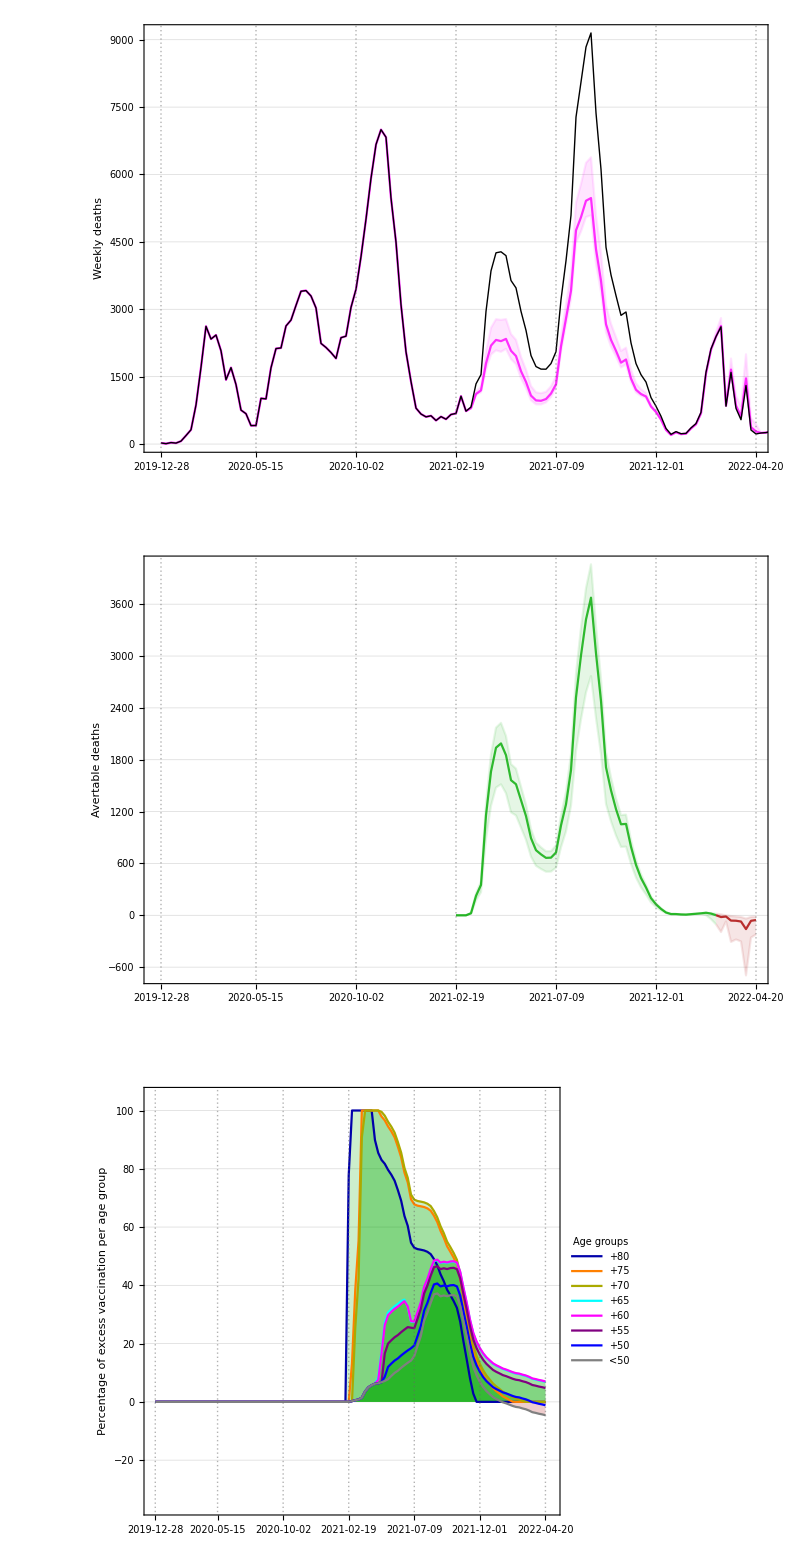

```mathematica
GraphicsGrid[{{p1},{p2},{p3}},ImagePadding->All,ImageSize->800]
```